```mathematica
sc1=Import["C:\\Users\\matane\\Desktop\\לימודים\\סמסטר ח\\A_ex4_final_movies\\ant_man\\CSV_files\\AB.csv"];
```

```mathematica
Grid[sc1,Frame->All];
```

------names charcater------

```mathematica
Union[sc1[[;;,2]]]
```

{Alpha Guard,Cab Driver,Carson,Cassie Lang,Cell Phone,Computer,Cop on Speaker,Dale,Darren Cross,Dave,Detective,Dr. Hank Pym,Frank,Gale,greatest allies,Hideous Rabbit,Hope van Dyne,Howard Stark,Ice Cream Store Customer,Kurt,Luis,Maggie Lang,Mitchell Carson,Paxton,Peachy,Peggy Carter,Police Radio,Pool BBQ Dad,Pym Tech Employee,Pym Tech Gate Guard,Pym Tech Security Guard,Sam Wilson,Scot Lang,Scott,Scott Lang,Speaker,Steve Rogers,Voice over Radio}

```mathematica
SortBy[Tally[sc1[[;;,2]]],Last]
```

{{Cab Driver,1},{Carson,1},{Cell Phone,1},{Cop on Speaker,1},{greatest allies,1},{Police Radio,1},{Pool BBQ Dad,1},{Pym Tech Employee,1},{Pym Tech Gate Guard,1},{Scot Lang,1},{Scott,1},{Speaker,1},{Voice over Radio,1},{Hideous Rabbit,2},{Pym Tech Security Guard,2},{Alpha Guard,3},{Computer,3},{Detective,3},{Ice Cream Store Customer,3},{Peachy,3},{Peggy Carter,3},{Steve Rogers,3},{Gale,4},{Frank,5},{Howard Stark,5},{Mitchell Carson,8},{Dale,11},{Sam Wilson,13},{Maggie Lang,16},{Cassie Lang,24},{Kurt,29},{Dave,34},{Paxton,46},{Darren Cross,56},{Luis,86},{Hope van Dyne,91},{Dr. Hank Pym,149},{Scott Lang,253}}

```mathematica
ch = sc1[[;;,2]];
```

```mathematica
e1=Table[ch[[i]]<->ch[[i+1]],{i,1,Length[ch]-1}];
e2=Table[ch[[i]]->ch[[i+1]],{i,1,Length[ch]-1}];
```

```mathematica
v1 = Union[ch];
```

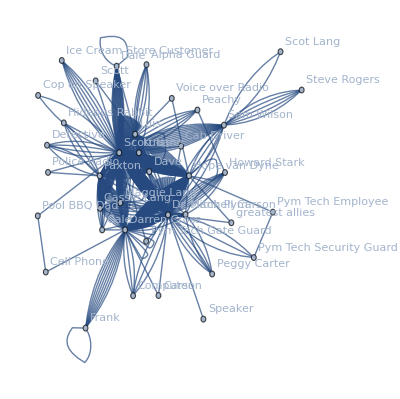

```mathematica
UndirectedWeightedGraph1=Graph[v1,e1,VertexLabels->"Name", ImageSize->Full]
UndirectedNonWeightedGraph2=SimpleGraph[UndirectedWeightedGraph1, ImageSize->Full];
DirectedWeightedGraph3=Graph[v1,e2,VertexLabels->"Name", ImageSize->Full];
DirectedNonWeightedGraph4=SimpleGraph[DirectedWeightedGraph3, ImageSize->Full];
```

THE 4 MAIN CHARACTHERS - ant_man
VM1our  = what we think
VM1 =  what algo found

```mathematica
VM1our = {"Scott Lang","Dr. Hank Pym", "Hope van Dyne","Darren Cross"}
(*VM1our = {"Scott Lang","Dr. Hank Pym", "Hope van Dyne","Darren Cross"}*)
```

```mathematica
PageRankCentrality[UndirectedWeightedGraph1,0.85];
SortBy[Transpose[{VertexList[UndirectedWeightedGraph1],PageRankCentrality[UndirectedWeightedGraph1,0.85]}],Last]
```

{{Speaker,0.00441088},{Scott,0.00480223},{Voice over Radio,0.00482903},{Cop on Speaker,0.00483306},{greatest allies,0.0048497},{Cab Driver,0.00485373},{Pym Tech Gate Guard,0.00485373},{Police Radio,0.00487294},{Carson,0.00490941},{Scot Lang,0.00550158},{Hideous Rabbit,0.00583841},{Pym Tech Employee,0.00606856},{Alpha Guard,0.00648195},{Ice Cream Store Customer,0.00660443},{Detective,0.00668421},{Computer,0.00683348},{Peachy,0.0069765},{Peggy Carter,0.00720832},{Pool BBQ Dad,0.00766403},{Cell Phone,0.00770311},{Gale,0.00772602},{Steve Rogers,0.00783291},{Pym Tech Security Guard,0.00791705},{Frank,0.00793555},{Howard Stark,0.0095872},{Dale,0.0127734},{Mitchell Carson,0.0132414},{Maggie Lang,0.0178895},{Sam Wilson,0.0237703},{Cassie Lang,0.0265607},{Kurt,0.0292029},{Dave,0.0335912},{Paxton,0.0522487},{Darren Cross,0.0621688},{Luis,0.0833726},{Hope van Dyne,0.0929262},{Dr. Hank Pym,0.153778},{Scott Lang,0.240699}}

```mathematica
(*{"Darren Cross",0.06216878377246405},{"Luis",0.08337264400653416},{"Hope van Dyne",0.09292623646610768},{"Dr. Hank Pym",0.15377760829795145},{"Scott Lang",0.24069867338632997}*)
VM1 = {"Scott Lang","Dr. Hank Pym", "Hope van Dyne","Luis"(*"Darren Cross"*)} (*"Darren Cross" is the fifth*)
```

{Scott Lang,Dr. Hank Pym,Hope van Dyne,Luis}

```mathematica
q 5-8
```